```mathematica
(* We want the Feynman diagram for Compton scattering *)
```

```mathematica
(* Step 1: Load the FeynArts package *)
```

```mathematica
<<FeynArts`
```

FeynArts 3.10 (21 Jan 2019)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
(* Step 2: Generate topologies with 0 loops, 2 incoming particles, and 2 outgoing particles *)
```

```mathematica
mytops=CreateTopologies[0,2->2]
```

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][5]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]]

> Top. 1 aebe/cede/0.m, 1 diagram

> Top. 2 aebe/cfdf/ef.m, 1 diagram

> Top. 3 aebf/cedf/ef.m, 1 diagram

> Top. 4 aebf/cfde/ef.m, 1 diagram



FeynArtsGraphics[2→2][([T1] | [T2] | [T3]
[T4] | Null | Null
Null | Null | Null)]

```mathematica
Paint[mytops]
```

```mathematica
(* Step 3: Insert the fields. We have a photon (vector boson, V[1]) and electron (first generation fermion, F[1]) going to a photon and an electron and this is a QED process *)
```

```mathematica
mydiags=InsertFields[mytops,{V[1],F[1]}->{V[1],F[1]},Model->"QED",InsertionLevel->{Classes}]
```

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 1 Classes insertion

in total: 2 Classes insertions

TopologyList[Process→{V[1],F[1,{Gen2}]}→{V[1],F[1,{Gen4}]},Model→{QED},GenericModel→{Lorentz},InsertionLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][6],Field[5]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F[1,{Gen2}]]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][6],Field[5]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→-F[1,{Gen2}]]]]]

> Top. 1 aebe/cfdf/ef.m, 1 diagram

> Top. 2 aebf/cfde/ef.m, 1 diagram

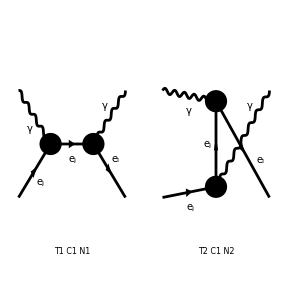

FeynArtsGraphics[{\gamma,ComposedChar[e,j]}→{\gamma,ComposedChar[e,l]}][([T1 C1 N1] | [T2 C1 N2] | Null
Null | Null | Null
Null | Null | Null)]

```mathematica
Paint[mydiags]
```

```mathematica
(* Step 4: Extract the diagram corresponding to Compton scattering *)
```

```mathematica
compton=DiagramExtract[mydiags,1]
```

TopologyList[Process→{V[1],F[1,{Gen2}]}→{V[1],F[1,{Gen4}]},Model→{QED},GenericModel→{Lorentz},InsertionLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][6],Field[5]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F[1,{Gen2}]]]]]

> Top. 1 aebe/cfdf/ef.m, 1 diagram

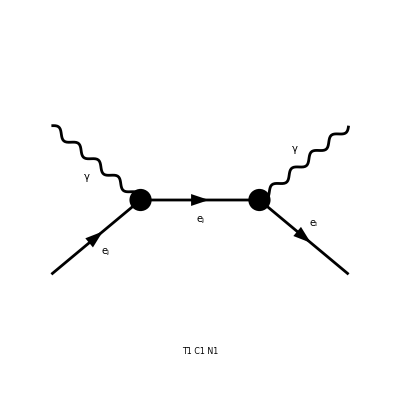

FeynArtsGraphics[{\gamma,ComposedChar[e,j]}→{\gamma,ComposedChar[e,l]}][([T1 C1 N1] | Null | Null
Null | Null | Null
Null | Null | Null)]

```mathematica
Paint[compton]
```